### LECs definition

```mathematica
hbarc=197.3161329;
mN=938.91852/hbarc;
λ={0.05,0.1,0.16,0.2,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.9,0.95,1,1.05,1.1,1.2,1.5,2,3,4,6,10};
CC={-1.552,-2.242,-3.440,-4.040,-6.397,-7.808,-9.310,-10.976,-12.782,-14.726,-16.809,-19.032,-21.394,-23.894,-26.536,-32.234,-35.291,-38.489,-41.824,-45.299,-52.666,-78.111,-131.646,-280.457,-484.921,-1060.797,-2880.387};
DD={-0.324,-0.246,0.019,0.223,1.207,1.981,2.828,3.913,5.209,6.718,8.468,10.463,12.734,15.276,18.137,24.813,28.664,32.911,37.527,42.570,53.971,100.476,232.413,854.107,2495.364,16915.630,756723.220};
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

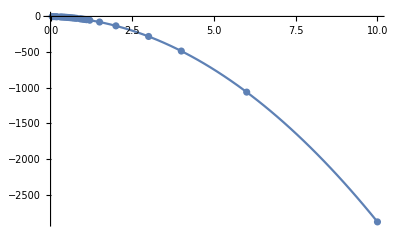

```mathematica
CL=Interpolation[Transpose[{λ,CC}]];
Plot[CL[x],{x,0,10}];
Show[%,ListPlot[Transpose[{λ,CC}]]]
```

InterpolatingFunction::dmval: Input value {0.000143} lies outside the range of data in the interpolating function. Extrapolation will be used.

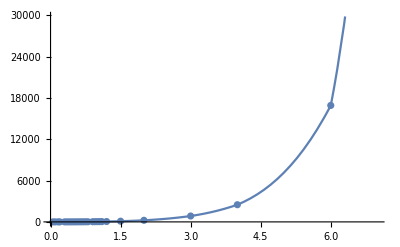

```mathematica
DL=Interpolation[Transpose[{λ,DD}]];
Plot[DL[x],{x,0,7}];
Show[%,ListPlot[Transpose[{λ,DD}]]]
```

## |A| - |1|

### V̂=𝟙 (norm & exchange kernel)

```mathematica
ClearAll;

ϵr2[A_?NumberQ]:=(3- A^-1);
ϵrr[A_?NumberQ]:=2 (1-A^-1);

MnoIntDi[nbr_?NumberQ]:=4 a IdentityMatrix[nbr-1]+(ConstantArray[2 a,{nbr-1,nbr-1}]-2 a IdentityMatrix[nbr-1]); 

MnoIntEx[nbr_?NumberQ]:=a ϵr2[nbr] IdentityMatrix[nbr-1]+(ConstantArray[a/2 ϵrr[nbr],{nbr-1,nbr-1}]-a/2 ϵrr[nbr] IdentityMatrix[nbr-1]); 
NnoIntEx[nbr_?NumberQ]:=ConstantArray[a nbr^-1 R+I s (1+nbr^-1),(nbr-1)];

dbg=1;testA=15;
For[nbr1=Switch[dbg==1,True,testA,False,2],nbr1<Switch[dbg==1,True,testA+1,False,9],nbr1++,{
Assuming[Λ^2>a&&a≥0&&a∈Reals&&Λ∈Reals&&Λ≥0&&R∈Reals&&R≥0&&r∈Reals&&r≥0,

Mex=MnoIntEx[nbr1]; 
Nex=NnoIntEx[nbr1];

Mdi=MnoIntDi[nbr1];

Kα=Simplify[CoefficientList[Simplify[ 1/2 Nex.Inverse[Mex].Nex],s]];

MexS=-2 Kα[[3]];
NexS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2;

If[dbg==2,Print["A = ",nbr1,"   ",Grid[Mex/MatrixForm,Nex//MatrixForm]],Sinn=1];
If[dbg==2,Print["A = ",nbr1,"   ",Kα],Sinn=1];
If[dbg==2,Print["A = ",nbr1,"   ",MexS,"   ",NexS],Sinn=1];

FakDi=Det[Mdi];
FakEx=Simplify[Det[Mex] MexS];
ExpEx=Simplify[MonomialList[(1/2 NexS^2/MexS+expR2),R]];

Print["A = ",nbr1,"   ;   |M_norm| =  ",Expand[Simplify[FakDi]],"\n            |M_exch| =  ",Expand[Simplify[FakEx]],"  ;  α_𝟙 =  ",ExpEx[[1]],"  ;  β_𝟙 =   ",ExpEx[[2]],";  γ_𝟙 =   ",ExpEx[[3]],"\n"];
]
}]
```

A = 15   ;   |M_norm| =  245760 a^14
            |M_exch| =  (29360128 a^13)/225  ;  α_𝟙 =  -(1695 a R^2)/3584  ;  β_𝟙 =   -(225 a r R)/1792;  γ_𝟙 =   -(1695 a r^2)/3584

#### Recurrence relations for norm and Exchange Kernels

```mathematica
Clear[A,Λ,a,nbr1,R,r];
dbg=1;
normfac[A_]:=FindSequenceFunction[{4,12,32,80,192,448,1024,2304,5120},A-1];

fz[A_]:=FindSequenceFunction[{9,64,75 4,1152,980 4,12288,567 8^2,102400,69696 4},A-1];
fn[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];

az[A_]:=FindSequenceFunction[{5,15,34,65,111,175,260,369},A-1];
abcn[A_]:=FindSequenceFunction[{9,32,75,144,245,384,567,800},A-1];
bz[A_]:=FindSequenceFunction[{8,18,32,50,72,98,128,162},A-1];

alphaNormEx[A_,a_]:=Simplify[a az[A]/abcn[A]];
betaNormEx[A_,a_]:=Simplify[a bz[A]/abcn[A]];
gammaNormEx[A_,a_]:=Simplify[a gz[A]/abcn[A]];
gz=az; (* hermiticity contraint *)

ExpoNormEx[A_,a_,R_,r_]:=Exp[-R^2 alphaNormEx[A,a]-betaNormEx[A,a] r R-gammaNormEx[A,a] r^2];

PreFacNormDiNenner[A_,a_]:=normfac[A] a^(A-1);
PreFacNormDi[A_,a_]:= ((2 Pi)^(A-1)/PreFacNormDiNenner[A,a])^(3/2);

PreFacNormExNenner[A_,a_]:=((fz[A]/fn[A]) a^(A-2));
PreFacNormEx[A_,a_]:=((2 Pi)^(A-1)/PreFacNormExNenner[A,a])^(3/2);

If[dbg==1,
Print[Row[{"A = ",testA,"   ;  |M_norm| =  ",PreFacNormDiNenner[testA,a],"\n           |M_exch| =  ",PreFacNormExNenner[testA,a],"  ;  α_EX =  ",
alphaNormEx[testA,a],"   ;  β_EX =  ",betaNormEx[testA,a],"    ;  γ_EX =  ",gammaNormEx[testA,a]
}]],Sinn=1];

Clear[A,a,R,r];
If[dbg==1,
Print["\nExKernel: Det(M_exch) e^(-SubscriptBox[α, 𝟙 - Ex] R^2 - SubscriptBox[β, 𝟙 - Ex] r^2 - SubscriptBox[γ, 𝟙 - Ex] Rr) =  (",PreFacNormExNenner[testA,a],")·",ExpoNormEx[testA,a,R,r]]
];
```

A = 15   ;  |M_norm| =  245760 a^14
           |M_exch| =  (29360128 a^13)/225  ;  α_EX =  (1695 a)/3584   ;  β_EX =  (225 a)/1792    ;  γ_EX =  (1695 a)/3584

ExKernel: Det(M_exch) e^(-SubscriptBox[α, 𝟙 - Ex] R^2 - SubscriptBox[β, 𝟙 - Ex] r^2 - SubscriptBox[γ, 𝟙 - Ex] Rr) =  ((29360128 a^13)/225)·ⅇ^(-(1695 a r^2)/3584-(225 a r R)/1792-(1695 a R^2)/3584)

#### performance version

```mathematica
PreFacNormDi[A,a]//InputForm
```

```mathematica
iPreFacNormDi[A_,a_]:=((a^(1-A)*Pi^(-1+A))/A)^(3/2);
```

```mathematica
PreFacNormEx[A,a]//InputForm
```

```mathematica
ifNormEx[A_,a_]:=2*Sqrt[2]*((a^(2-A)*(1+2*(-1+A)+(-1+A)^2)*Pi^(-1+A))/((-1+A)*(1+A)^2))^(3/2);
```

```mathematica
alphaNormEx[A,a]//InputForm
```

```mathematica
ialfNormEx[A_,a_]:=(a*(A+A^3))/(2*(-1+A)*(1+A)^2);
```

```mathematica
betaNormEx[A,a]//InputForm
```

```mathematica
ibetNormEx[A_,a_]:=(2*a*A^2)/((-1+A)*(1+A)^2);
```

```mathematica
gammaNormEx[A,a]//InputForm
```

```mathematica
igamNormEx[A_,a_]:=(a*(A+A^3))/(2*(-1+A)*(1+A)^2);
```

### V̂=C_2· ∑_(i<A)δ_Λ((r̄)_i+R) (2NI direct interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=1;testA=3;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{
Assuming[Λ^2>a&&a≥0&&a∈Reals&&Λ∈Reals&&Λ≥0&&R∈Reals&&R≥0&&r∈Reals&&r≥0,

M2Di=MnoIntDi[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N2Di=Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M2Di;
inhom=N2Di;

Kα=Simplify[ 1/2 inhom.Inverse[mat].inhom];

expR2=Kα-Λ^2/4 R^2;
PreFak=Simplify[Det[mat]];
Expo=Simplify[MonomialList[expR2,Λ]];

Print["A = ",nbr1,"      ;    |M| =  ",Expand[Simplify[PreFak]],"    ;  α =   ",Simplify[Expo[[1]]]];
]
}]
```

A = 3      ;    |M| =  12 a^2+2 a Λ^2    ;  α =   -(3 a R^2 Λ^2)/(2 (6 a+Λ^2))

#### Recurrence relations 2NI Direct

```mathematica
Clear[A,Λ,a,R,x];
sa[A_]:=FindSequenceFunction[{4,12,32,80,192,448},A-1];
saΛ[A_]:=FindSequenceFunction[{1/2,2,6,16,40,96},A-1];
sexpn1[A_]:=FindSequenceFunction[{8,12,16,20,24,28},A-1];
alpha2NIDi[A_,a_,Λ_]:=A Λ^2/(sexpn1[A]+(A-1) Λ^2/a);

PreFac2NIDiNenner[A_,a_,Λ_]:=sa[A] a^(A-1)+saΛ[A] a^(A-2) Λ^2;
PreFac2NIDi[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-1)/PreFac2NIDiNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];
Expo2NIDi[A_,a_,Λ_,R_]:=Exp[-alpha2NIDi[A,a,Λ] R^2];

If[dbg==1,
Print[Row[{"A = ",testA,"   ;  |M| =  ",PreFac2NIDiNenner[testA,a,Λ],"  ;  α =  ",
alpha2NIDi[testA,a,Λ]
}]],Sinn=1];

Clear[A,a,Λ,R,x];
If[dbg==1,
Print["\n2NI Direct:          Det(M) e^(-α R^2) =  (",PreFac2NIDiNenner[testA,a,Λ],")·",Expo2NIDi[testA,a,Λ,R]]
];
```

A = 3   ;  |M| =  12 a^2+2 a Λ^2  ;  α =  (3 Λ^2)/(12+(2 Λ^2)/a)

2NI Direct:          Det(M) e^(-α R^2) =  (12 a^2+2 a Λ^2)·ⅇ^(-(3 R^2 Λ^2)/(12+(2 Λ^2)/a))

#### performance version

```mathematica
(PreFac2NIDi[A,a,Λ] Expo2NIDi[A,a,Λ,R])//InputForm
```

(8*((a^(2 - A)*Pi^(-1 + A))/(4*a*A + (-1 + A)*Λ^2))^(3/2))/(E^((A*R^2*Λ^2)/(4*A + ((-1 + A)*Λ^2)/a))*
  ((a^(1 - A)*Pi^(-1 + A))/A)^(3/2))

```mathematica
i2NIDi[A_,a_,Λ_,R_]:=(8*((a^(2-A)*Pi^(-1+A))/(4*a*A+(-1+A)*Λ^2))^(3/2))/(E^((A*R^2*Λ^2)/(4*A+((-1+A)*Λ^2)/a))*((a^(1-A)*Pi^(-1+A))/A)^(3/2));
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i-(r̄)_j)δ_Λ((r̄)_i+R)] (3NI (ARM) direct interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=11;testA=3;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,7],nbr1++,{
Assuming[Λ^2>a&&a≥0&&a∈Reals&&Λ∈Reals&&Λ≥0&&R∈Reals&&R≥0&&r∈Reals&&r≥0,

M3armDi=MnoIntDi[nbr1]+Table[If[i==j==1,Λ^2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[(i==1&&j==2)||(i==2&&j==1),-Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3armDi=Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3armDi;
inhom=N3armDi;

Kα=Simplify[ 1/2 inhom.Inverse[mat].inhom];

expR2=Kα-Λ^2/4 R^2;
PreFak=Simplify[Det[mat]];
Expo=Simplify[MonomialList[expR2,Λ]];

Print["A = ",nbr1,"      ;    |M_𝟙| =  ",Expand[Simplify[PreFak]],"    ;  α_𝟙 =   ",Simplify[Expo[[1]]]];
]
}]
```

A = 3      ;    |M_𝟙| =  12 a^2+8 a Λ^2+Λ^4/4    ;  α_𝟙 =   -(6 a R^2 Λ^2 (2 a+Λ^2))/(48 a^2+32 a Λ^2+Λ^4)

A = 4      ;    |M_𝟙| =  32 a^3+22 a^2 Λ^2+a Λ^4    ;  α_𝟙 =   -(4 a R^2 Λ^2 (2 a+Λ^2))/(32 a^2+22 a Λ^2+Λ^4)

A = 5      ;    |M_𝟙| =  80 a^4+56 a^3 Λ^2+3 a^2 Λ^4    ;  α_𝟙 =   -(10 a R^2 Λ^2 (2 a+Λ^2))/(80 a^2+56 a Λ^2+3 Λ^4)

A = 6      ;    |M_𝟙| =  192 a^5+136 a^4 Λ^2+8 a^3 Λ^4    ;  α_𝟙 =   -(3 a R^2 Λ^2 (2 a+Λ^2))/(24 a^2+17 a Λ^2+Λ^4)

#### Recurrence relations 3NI ARM Direct

```mathematica
Clear[A];
dbg=1;
c3armdief1[A_]:=FindSequenceFunction[{12,32,80,192,448,1024,2304},A-2];
c3armdief2[A_]:=FindSequenceFunction[{8,22,56,136,320,736,1664},A-2];
c3armdief3[A_]:=FindSequenceFunction[{1/4,1,3,8,20,48,112,256},A-2];

c3armdiexpz1[A_]:=FindSequenceFunction[{12,16,20,24,28,32,36},A-2];
c3armdiexpz2[A_]:=FindSequenceFunction[{6,8,10,12},A-2];

c3armdiexpn1[A_]:=FindSequenceFunction[{48,64,80,96,112,128},A-2];
c3armdiexpn2[A_]:=FindSequenceFunction[{32,44,56,68,80,92,104},A-2];
c3armdiexpn3[A_]:=FindSequenceFunction[{1,2,3,4,5,6,7,8},A-2];

alpha3NIarmDi[A_,a_,Λ_]:=Λ^2 (c3armdiexpz1[A] a^2+c3armdiexpz2[A] a Λ^2)/(c3armdiexpn1[A] a^2+c3armdiexpn2[A] a Λ^2+c3armdiexpn3[A] Λ^4);
PreFac3NIarmDiNenner[A_,a_,Λ_]:=(c3armdief1[A] a^(A-1)+c3armdief2[A] a^(A-2) Λ^2+c3armdief3[A] a^(A-3) Λ^4);
PreFac3NIarmDi[A_,a_,Λ_]:=(Simplify[((2 Pi)^(A-1)/PreFac3NIarmDiNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)]);
Expo3NIarmDi[A_,a_,Λ_,R_]:=Exp[- alpha3NIarmDi[A,a,Λ] R^2];

If[dbg==1,
Print[Row[{"A = ",testA,"   ;  |M| =  ",PreFac3NIarmDiNenner[testA,a,Λ],"  ;  α =  ",
alpha3NIarmDi[testA,a,Λ]
}]],Sinn=1];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-ARM Direct:            Det(M) e^(-α R^2) =    (",PreFac3NIarmDiNenner[testA,a,Λ],")·",Expo3NIarmDi[testA,a,Λ,R]]
];
```

A = 3   ;  |M| =  12 a^2+8 a Λ^2+Λ^4/4  ;  α =  (Λ^2 (12 a^2+6 a Λ^2))/(48 a^2+32 a Λ^2+Λ^4)

3NI-ARM Direct:            Det(M) e^(-α R^2) =    (12 a^2+8 a Λ^2+Λ^4/4)·ⅇ^(-(R^2 Λ^2 (12 a^2+6 a Λ^2))/(48 a^2+32 a Λ^2+Λ^4))

#### performance version

```mathematica
(PreFac3NIarmDi[A,a,Λ] Expo3NIarmDi[A,a,Λ,R])//InputForm
```

(64*((a^(3 - A)*Pi^(-1 + A))/(16*a^2*A + 4*a*(-1 + 3*A)*Λ^2 + (-2 + A)*Λ^4))^(3/2))/
 (E^((R^2*Λ^2*(4*a^2*A + 2*a*A*Λ^2))/(16*a^2*A + 4*a*(5 + 3*(-2 + A))*Λ^2 + (-2 + A)*Λ^4))*((a^(1 - A)*Pi^(-1 + A))/A)^(3/2))

```mathematica
i3NIarmDi[A_,a_,Λ_,R_]:=(64*((a^(3-A)*Pi^(-1+A))/(16*a^2*A+4*a*(-1+3*A)*Λ^2+(-2+A)*Λ^4))^(3/2))/(E^((R^2*Λ^2*(4*a^2*A+2*a*A*Λ^2))/(16*a^2*A+4*a*(5+3*(-2+A))*Λ^2+(-2+A)*Λ^4))*((a^(1-A)*Pi^(-1+A))/A)^(3/2));
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i+R)δ_Λ((r̄)_j+R)] (3NI (STAR) direct interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=1;testA=9;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{
Assuming[Λ^2>a&&a≥0&&a∈Reals&&Λ∈Reals&&Λ≥0&&R∈Reals&&R≥0&&r∈Reals&&r≥0,

M3starDi=MnoIntDi[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3starDi=Table[If[i==1||i==2,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3starDi;
inhom=N3starDi;

Kα=Simplify[ 1/2 inhom.Inverse[mat].inhom];

expR2=Kα-Λ^2/2 R^2;
PreFak=Simplify[Det[mat]];
Expo=Simplify[MonomialList[expR2,Λ]];

Print["A = ",nbr1,"      ;    |M| =  ",Expand[Simplify[PreFak]],"    ;  α =   ",Simplify[Expo[[1]]]];
]
}]
```

A = 9      ;    |M| =  2304 a^8+1024 a^7 Λ^2+112 a^6 Λ^4    ;  α =   -(18 a R^2 Λ^2)/(36 a+7 Λ^2)

#### Recurrence relations 3NI STAR Direct

```mathematica
Clear[A];
sl0s[A_]:=FindSequenceFunction[{4,12,32,80,192,448},A-1];
sl2s[A_]:=FindSequenceFunction[{4,12,32,80,192,448,1024},A-2];
sl4s[A_]:=FindSequenceFunction[{1/4,1,3,8,20,48,112,256},A-2];

sexpz1s[A_]:=FindSequenceFunction[{6,8,10,12,14,16,18},A-2];
sexpn0s[A_]:=FindSequenceFunction[{12,16,20,24,28,32,36,40},A-2];
sexpn2s[A_]:=FindSequenceFunction[{1,2,3,4,5,6,7,8},A-2];

alpha3NIstarDi[A_,a_,Λ_]:=a Λ^2 sexpz1s[A]/(sexpn0s[A] a+sexpn2s[A] Λ^2);
PreFac3NIstarDiNenner[A_,a_,Λ_]:=(sl0s[A] a^(A-1)+sl2s[A] a^(A-2) Λ^2+sl4s[A] a^(A-3) Λ^4);
PreFac3NIstarDi[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-1)/PreFac3NIstarDiNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];
Expo3NIstarDi[A_,a_,Λ_,R_]:=Exp[-alpha3NIstarDi[A,a,Λ] R^2];

If[dbg==1,
Print[Row[{"A = ",testA,"   ;  |M| =  ",PreFac3NIstarDiNenner[testA,a,Λ],"  ;  α =  ",
alpha3NIstarDi[testA,a,Λ]
}]],Sinn=1];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-STAR Direct:         Det(M) e^(-α R^2) =  (",PreFac3NIstarDiNenner[testA,a,Λ],")·",Expo3NIstarDi[testA,a,Λ,R]]
];
```

A = 9   ;  |M| =  2304 a^8+1024 a^7 Λ^2+112 a^6 Λ^4  ;  α =  (18 a Λ^2)/(36 a+7 Λ^2)

3NI-STAR Direct:         Det(M) e^(-α R^2) =  (2304 a^8+1024 a^7 Λ^2+112 a^6 Λ^4)·ⅇ^(-(18 a R^2 Λ^2)/(36 a+7 Λ^2))

performance version

#### (PreFac3NIstarDi[A, a, Λ] Expo3NIstarDi[A, a, Λ, R]) // InputForm

```mathematica
i3NIstarDi[A_,a_,Λ_,R_]:=(64*((a^(3-A)*Pi^(-1+A))/((4*a+Λ^2)*(4*a*A+(-2+A)*Λ^2)))^(3/2))/(E^((2*a*A*R^2*Λ^2)/(4*a*A+(-2+A)*Λ^2))*((a^(1-A)*Pi^(-1+A))/A)^(3/2));
```

#### Plot direct interaction kernels

```mathematica
Clear[A,a,Λ,R];
AA1=4;aa1=3.;Lam1=4;
AA2=4;aa2=3.;Lam2=4;
Rmax=2;
(*amx=20;
ListPlot[{Table[(n/(n+1)) CL[Lam1] (n-1) PreFac2NIDi[n,aa1,Lam1],{n,2,amx}],Table[1/2 DL[Lam1] (n/(n+1)) (n-1) (n-2) (PreFac3NIarmDi[n,aa1,Lam1]+PreFac3NIstarDi[n,aa1,Lam1]),{n,2,amx}]},PlotLegends->{"PreFaktor (V̂)_(2 NI) ; direct","PreFaktor (V̂)_(3 NI - arm)+(V̂)_(3 NI - star) ; direct"},Joined->{True},PlotStyle->{Orange,Red}]*)
myStyle4=Grid[{{Style["A_1 = "<>ToString[AA1]<>"   a_1 = "<>ToString[aa1]<>" fm^-2"<>"   Λ_1 = "<>ToString[Lam1]<>" fm^-1     (V̂)_(2  NI)+(V̂)_(3  NI)",Black]},{Style["A_2 = "<>ToString[AA2]<>"   a_2 = "<>ToString[aa2]<>" fm^-2"<>"   Λ_2 = "<>ToString[Lam2]<>" fm^-1     (V̂)_(2  NI)",Blue]}}];
Animate[
Plot[{
(AA1/(AA1+1)) (0.5 DL[Lam1] (AA1-1) (AA1-2) (i3NIarmDi[AA1,aa1,Lam1,r]+i3NIstarDi[AA1,aa1,Lam1,r])+
CL[Lam1] (AA1-1) i2NIDi[AA1,aa1,Lam1,r]),(AA1/(AA1+1)) (0.5 DL[Lam2] (AA2-1) (AA2-2) (i3NIarmDi[AA2,aa2,Lam2,r]+i3NIstarDi[AA2,aa2,Lam2,r])+CL[Lam2] (AA2-1) i2NIDi[AA2,aa2,Lam2,r])
},{r,0,Rmax},PlotPoints->40,MaxRecursion->0,PlotLegends->{},PlotLabel->myStyle4,PlotStyle->{{Black,Dashed},{Blue,Dashed}},AxesLabel->{"R"}],
{Lam1,1.,15.2},DefaultDuration->3,AnimationRepetitions->1]
```

### V̂=C_2· ∑_(i<A)δ_Λ((r̄)_i+R) (2NI EX interaction kernel)

```mathematica
Clear[A,a,nbr1];
dbg=1;testA=9;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{
Assuming[Λ^2>a&&a≥0&&a∈Reals&&Λ∈Reals&&Λ≥0&&R∈Reals&&R≥0&&r∈Reals&&r≥0,

M2Ex=MnoIntEx[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N2Ex=NnoIntEx[nbr1]+Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M2Ex;
inhom=N2Ex;

Kα=Simplify[CoefficientList[Simplify[ 1/2 inhom.Inverse[mat].inhom],s]];

matS=-2 Kα[[3]];
inhomS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2-Λ^2/4 R^2;

PreFak=Simplify[Det[mat] matS];

Expo=Simplify[MonomialList[(1/2 inhomS^2/matS+expR2),R]];

Print["A = ",nbr1,"   ;  |M_EX| =  ",Expand[Simplify[PreFak]],"  ;  α_EX =  ",Expo[[1]],"   ;  β_EX =  ",Simplify[Expo[[2]]],"    ;  γ_EX =  ",Simplify[Expo[[3]]]];
]
}]
```

#### Recurrence relations 2NI Exchange

```mathematica
Clear[A,Λ,a,R];dbg=1;
c2exexpn1[A_]:=FindSequenceFunction[{16,25,36,49,64,81,100,121},A-2];
c2exexpn2[A_]:=FindSequenceFunction[{8,12,16,20,24,28,32},A-2];
c2exexpn3[A_]:=FindSequenceFunction[{1,2,3,4,5,6,7},A-2];

c2exalfz1[A_]:=FindSequenceFunction[{12 5,4 34,5 52,12 37,14 50,8 130},A-2];
c2exalfz2[A_]:=FindSequenceFunction[{12 4,4 27,5 41,12 29,14 39,8 101},A-2];

c2exbetz1[A_]:=FindSequenceFunction[{9 4,64,100,36 4,49 4,128 2},A-2];

c2exgamz2[A_]:=FindSequenceFunction[{12,4 7,55,12 8,14 11},A-2];

c2exfakz1[A_]:=FindSequenceFunction[{9,64,75 4,1152,980 4,12288,567 64,102400,69696 4,737280},A-1];
c2exfakn1[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];
c2exfakz2[A_]:=FindSequenceFunction[{0,8,50,216,196 4,2560,243 32,22400,15488 4,165888},A-1];
c2exfakn2[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];

PreFac2NIExNenner[A_,a_,Λ_]:=(c2exfakz1[A]/c2exfakn1[A]) a^(A-2)+(c2exfakz2[A]/c2exfakn2[A]) a^(A-3) Λ^2;
PreFac2NIEx[A_,a_,Λ_]:=((2 Pi)^(A-2)/PreFac2NIExNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1);

alf2NIEx[A_,a_,Λ_]:=(c2exalfz1[A] a^2+c2exalfz2[A] a Λ^2)/(c2exexpn1[A] (c2exexpn2[A] a+c2exexpn3[A] Λ^2));
bet2NIEx[A_,a_,Λ_]:=a c2exbetz1[A] ((2 a+Λ^2)/(c2exexpn1[A] (c2exexpn2[A] a+c2exexpn3[A] Λ^2)));
gam2NIEx[A_,a_,Λ_]:=(c2exalfz1[A] a^2+c2exgamz2[A] a Λ^2)/(c2exexpn1[A] (c2exexpn2[A] a+c2exexpn3[A] Λ^2));
Expo2NIEx[A_,a_,Λ_,R_,r_]:=Exp[-R^2 alf2NIEx[A,a,Λ]-R r bet2NIEx[A,a,Λ]-r^2 gam2NIEx[A,a,Λ]];

If[dbg==1,
tmp=CoefficientList[Exponent[Expo2NIEx[testA,a,Λ,R,r],E],r];
Print[Row[{"A = ",testA,"   ;  |M_EX| =  ",PreFac2NIExNenner[testA,a,Λ],"  ;  α_EX =  ",
tmp[[1]]/.R^2->"","   ;  β_EX =  ",tmp[[2]]/.R->"","    ;  γ_EX =  ",tmp[[3]]
}]],Sinn=1];


Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n2NI: Det(M_(2  NI - Ex)) e^(-SubscriptBox[α, 2  Ni - Ex] R^2 - SubscriptBox[β, 2  Ni - Ex] r^2 - SubscriptBox[γ, 2  Ni - Ex] Rr) =  (",PreFac2NIExNenner[testA,a,Λ],")·",Expo2NIEx[testA,a,Λ,R,r]]
];
```

#### performance version

```mathematica
(PreFac2NIEx[A,a,Λ] Expo2NIEx[A,a,Λ,R,r])//InputForm
```

```mathematica
i2NIEx[A_,a_,Λ_,R_,r_]:=(2*Sqrt[2]*E^((-4*a*(4+4*(-2+A)+(-2+A)^2)*r*R*(2*a+Λ^2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-2+A)*Λ^2))-(r^2*(2*a^2*(10+13*(-2+A)+6*(-2+A)^2+(-2+A)^3)+(a*(8+10*(-2+A)+5*(-2+A)^2+(-2+A)^3)*Λ^2)/2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-2+A)*Λ^2))-(R^2*(2*a^2*(10+13*(-2+A)+6*(-2+A)^2+(-2+A)^3)+(a*(32+42*(-2+A)+19*(-2+A)^2+3*(-2+A)^3)*Λ^2)/2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-2+A)*Λ^2)))*((2*Pi)^(-2+A)/((2^(-2+A)*a^(-2+A)*(-1+A)*(1+A)^2)/(1+2*(-1+A)+(-1+A)^2)+(2^(-4+A)*a^(-3+A)*(-2+A)*(1+A)^2*Λ^2)/(1+2*(-1+A)+(-1+A)^2)))^(3/2))/((a^(1-A)*Pi^(-2+A))/A)^(3/2);
```

```mathematica
PreFac2NIEx[A,a,Λ]//InputForm
```

```mathematica
if2NIEx[A_,a_,Λ_]:=((2*Pi)^(-2+A)/((2^(-2+A)*a^(-2+A)*(-1+A)*(1+A)^2)/(1+2*(-1+A)+(-1+A)^2)+(2^(-4+A)*a^(-3+A)*(-2+A)*(1+A)^2*Λ^2)/(1+2*(-1+A)+(-1+A)^2)))^(3/2)/((a^(1-A)*Pi^(-1+A))/A)^(3/2);
```

```mathematica
alf2NIEx[A,a,Λ]//InputForm
```

```mathematica
ialf2NIEx[A_,a_,Λ_]:=(2*a^2*(10+13*(-2+A)+6*(-2+A)^2+(-2+A)^3)+(a*(32+42*(-2+A)+19*(-2+A)^2+3*(-2+A)^3)*Λ^2)/2)/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
bet2NIEx[A,a,Λ]//InputForm
```

```mathematica
ibet2NIEx[A_,a_,Λ_]:=(4*a*(4+4*(-2+A)+(-2+A)^2)*(2*a+Λ^2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-2+A)*Λ^2));
```

```mathematica
gam2NIEx[A,a,Λ]//InputForm
```

```mathematica
igam2NIEx[A_,a_,Λ_]:=(2*a^2*(10+13*(-2+A)+6*(-2+A)^2+(-2+A)^3)+(a*(8+10*(-2+A)+5*(-2+A)^2+(-2+A)^3)*Λ^2)/2)/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-2+A)*Λ^2));
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i-(r̄)_j)δ_Λ((r̄)_i+R)] (3NI (ARM) EX interaction kernel)

```mathematica
Clear[A,a,nbr1,Λ];
dbg=1;testA=13;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,13],nbr1++,{
Assuming[Λ^2>a&&a≥0&&a∈Reals&&Λ∈Reals&&Λ≥0&&R∈Reals&&R≥0&&r∈Reals&&r≥0,

M3armEx=MnoIntEx[nbr1]+Table[If[i==j==1,Λ^2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[(i==1&&j==2)||(i==2&&j==1),-Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3armEx=NnoIntEx[nbr1]+Table[If[i==1,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3armEx;
inhom=N3armEx;

Kα=Simplify[CoefficientList[Simplify[ 1/2 inhom.Inverse[mat].inhom],s]];

matS=-2 Kα[[3]];
inhomS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2-Λ^2/4 R^2;

PreFak=Simplify[Det[mat] matS];

Expo=Simplify[MonomialList[(1/2 inhomS^2/matS+expR2),R]];

Print["A = ",nbr1,"   ;  |M_EX| =  ",Expand[Simplify[PreFak]],"  ;  α_EX =  ",Expo[[1]],"   ;  β_EX =  ",Simplify[Expo[[2]]],"    ;  γ_EX =  ",Simplify[Expo[[3]]]];
]
}]
```

#### Recurrence relations 3NI Exchange

```mathematica
Clear[A,Λ,a,R];

c3armexfakz1[A_]:=FindSequenceFunction[{9,64,75 4,1152,980 4,12288,567 64,102400,69696 4},A-1];
c3armexfakz2[A_]:=FindSequenceFunction[{40,25 8,792,686 4,8704,405 64,73600,50336 4,534528,16 86528},A-2];
c3armexfakz3[A_]:=FindSequenceFunction[{0,25/4,36,49 3,512,405 4,1600 3,3388 4,36864,676 144},A-2];
c3armexfakn1[A_]:=FindSequenceFunction[{4,9,16,25,36,49,64},A-1];

c3armexexpn1[A_]:=FindSequenceFunction[{32,48,64,80,96,112,128},A-2];
c3armexexpn2[A_]:=FindSequenceFunction[{20,32,44,56,68,80,92},A-2];
c3armexexpn3[A_]:=FindSequenceFunction[{0,1,2,3,4,5,6,7},A-2];

c3armexalfz1[A_]:=FindSequenceFunction[{80,136,208,296,400,520},A-2];
c3armexalfz2[A_]:=FindSequenceFunction[{104,176,268,380,512,664},A-2];
c3armexalfz3[A_]:=FindSequenceFunction[{27,91/2,69,195/2,131,339/2},A-2];

c3armexbetz1[A_]:=FindSequenceFunction[{18,32,50,72,98},A-2];

c3armexgamz1[A_]:=FindSequenceFunction[{56,96,148,212,288,376,476},A-2];
c3armexgamz2[A_]:=FindSequenceFunction[{3,11/2,9,27/2,19,51/2},A-2];

PreFac3NIarmExNenner[A_,a_,Λ_]:=((c3armexfakz1[A]/c3armexfakn1[A]) a^(A-2)+(c3armexfakz2[A]/c3armexfakn1[A]) a^(A-3) Λ^2+(c3armexfakz3[A]/c3armexfakn1[A]) a^(A-4) Λ^4);
PreFac3NIarmEx[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-2)/PreFac3NIarmExNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];

alf3NIarmEx[A_,a_,Λ_]:=A a (c3armexalfz1[A] a^2+c3armexalfz2[A] a Λ^2+c3armexalfz3[A] Λ^4)/((A+1)^2 (c3armexexpn1[A] a^2+c3armexexpn2[A] a Λ^2+c3armexexpn3[A] Λ^4));
bet3NIarmEx[A_,a_,Λ_]:=a c3armexbetz1[A] (16 a^2+16 a Λ^2+3 Λ^4)/((A+1)^2 (c3armexexpn1[A] a^2+c3armexexpn2[A] a Λ^2+c3armexexpn3[A] Λ^4));
gam3NIarmEx[A_,a_,Λ_]:=a A (c3armexalfz1[A] a^2+c3armexgamz1[A] a Λ^2+c3armexgamz2[A] Λ^4)/((A+1)^2 (c3armexexpn1[A] a^2+c3armexexpn2[A] a Λ^2+c3armexexpn3[A] Λ^4));
Expo3NIarmEx[A_,a_,Λ_,R_,r_]:=Exp[-R^2 alf3NIarmEx[A,a,Λ]-R r bet3NIarmEx[A,a,Λ]-r^2 gam3NIarmEx[A,a,Λ]];

If[dbg==1,
tmp=CoefficientList[Exponent[Expo3NIarmEx[testA,a,Λ,R,r],E],r];
Print[Row[{"A = ",testA,"   ;  |M_EX| =  ",PreFac3NIarmExNenner[testA,a,Λ],"  ;  α_EX =  ",
tmp[[1]]/.R^2->"","   ;  β_EX =  ",tmp[[2]]/.R->"","    ;  γ_EX =  ",tmp[[3]]
}]],Sinn=1];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-ARM: Det(M_(3  NI - Ex)) e^(-SubscriptBox[α, 3  Ni - Ex] R^2 - SubscriptBox[β, 3  Ni - Ex] r^2 - SubscriptBox[γ, 3  Ni - Ex] Rr) =  (",PreFac3NIarmExNenner[testA,a,Λ],")·",Expo3NIarmEx[testA,a,Λ,R,r]]
];
```

#### performance version

```mathematica
(PreFac3NIarmEx[A,a,Λ] Expo3NIarmEx[A,a,Λ,R,r])//InputForm
```

```mathematica
i3NIarmEx[A_,a_,Λ_,R_,r_]:=(128*Sqrt[2]*E^((-2*a*(4+4*(-2+A)+(-2+A)^2)*r*R*(16*a^2+16*a*Λ^2+3*Λ^4))/((1+A)^2*(16*a^2*(-1+A)+4*a*(2+3*(-2+A))*Λ^2+(-3+A)*Λ^4))-(a*A*r^2*(8*a^2*(5+4*(-2+A)+(-2+A)^2)+2*a*(14+11*(-2+A)+3*(-2+A)^2)*Λ^2+((3+2*(-2+A)+(-2+A)^2)*Λ^4)/2))/((1+A)^2*(16*a^2*(-1+A)+4*a*(2+3*(-2+A))*Λ^2+(-3+A)*Λ^4))-(a*A*R^2*(8*a^2*(5+4*(-2+A)+(-2+A)^2)+2*a*(26+21*(-2+A)+5*(-2+A)^2)*Λ^2+((27+22*(-2+A)+5*(-2+A)^2)*Λ^4)/2))/((1+A)^2*(16*a^2*(-1+A)+4*a*(2+3*(-2+A))*Λ^2+(-3+A)*Λ^4)))*((a^(4-A)*A^2*Pi^(-2+A))/((1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4)))^(3/2))/((a^(1-A)*Pi^(-2+A))/A)^(3/2);
```

```mathematica
PreFac3NIarmEx[A,a,Λ]//InputForm
```

```mathematica
if3NIarmEx[A_,a_,Λ_]:=(64*((a^(4-A)*A^2*Pi^(-2+A))/((1+A)^2*(16*a^2*(-1+A)+4*a*(-4+3*A)*Λ^2+(-3+A)*Λ^4)))^(3/2))/((a^(1-A)*Pi^(-1+A))/A)^(3/2);
```

```mathematica
alf3NIarmEx[A,a,Λ]//InputForm
```

```mathematica
ialf3NIarmEx[A_,a_,Λ_]:=(a*A*(8*a^2*(5+4*(-2+A)+(-2+A)^2)+2*a*(26+21*(-2+A)+5*(-2+A)^2)*Λ^2+((27+22*(-2+A)+5*(-2+A)^2)*Λ^4)/2))/((1+A)^2*(16*a^2*(-1+A)+4*a*(2+3*(-2+A))*Λ^2+(-3+A)*Λ^4));
```

```mathematica
bet3NIarmEx[A,a,Λ]//InputForm
```

```mathematica
ibet3NIarmEx[A_,a_,Λ_]:=(2*a*(4+4*(-2+A)+(-2+A)^2)*(16*a^2+16*a*Λ^2+3*Λ^4))/((1+A)^2*(16*a^2*(-1+A)+4*a*(2+3*(-2+A))*Λ^2+(-3+A)*Λ^4));
```

```mathematica
gam3NIarmEx[A,a,Λ]//InputForm
```

```mathematica
igam3NIarmEx[A_,a_,Λ_]:=(a*A*(8*a^2*(5+4*(-2+A)+(-2+A)^2)+2*a*(14+11*(-2+A)+3*(-2+A)^2)*Λ^2+((3+2*(-2+A)+(-2+A)^2)*Λ^4)/2))/((1+A)^2*(16*a^2*(-1+A)+4*a*(2+3*(-2+A))*Λ^2+(-3+A)*Λ^4));
```

### V̂=D_1· ∑_(i<j<A) [δ_Λ((r̄)_i-(r̄)_j)δ_Λ((r̄)_i+R)] (3NI (STAR) EX interaction kernel)

```mathematica
Clear[A,a,nbr1,Λ];
dbg=11;testA=7;
For[nbr1=Switch[dbg==1,True,testA,False,3],nbr1<Switch[dbg==1,True,testA+1,False,15],nbr1++,{
Assuming[Λ^2>a&&a≥0&&a∈Reals&&Λ∈Reals&&Λ≥0&&R∈Reals&&R≥0&&r∈Reals&&r≥0,

M3armEx=MnoIntEx[nbr1]+Table[If[i==j==1,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}]+Table[If[i==j==2,Λ^2/2,0],{i,nbr1-1},{j,nbr1-1}];
N3armEx=NnoIntEx[nbr1]+Table[If[i==1||i==2,Λ^2 R/2,0],{i,nbr1-1}];

mat=M3armEx;
inhom=N3armEx;

Kα=Simplify[CoefficientList[Simplify[ 1/2 inhom.Inverse[mat].inhom],s]];

matS=-2 Kα[[3]];
inhomS=Kα[[2]]+I (R/nbr1+ r);
expR2=Kα[[1]]-a/2 (1-nbr1^-1) R^2-Λ^2/2 R^2;

PreFak=Simplify[Det[mat] matS];

Expo=Simplify[MonomialList[(1/2 inhomS^2/matS+expR2),R]];

Print["A = ",nbr1,"   ;  |M_EX| =  ",Expand[Simplify[PreFak]],"  ;  α_EX =  ",Expo[[1]],"   ;  β_EX =  ",Simplify[Expo[[2]]],"    ;  γ_EX =  ",Simplify[Expo[[3]]]];
]
}]
```

#### Recurrence relations for the pre- and exponential factors 3NI STAR Exchange

```mathematica
Clear[A,Λ,a,R];
dbg=1;
c3starexfakz1[A_]:=FindSequenceFunction[{64,75 4,1152,980 4,12288,567 64,102400,69696 4,737280},A-2];
c3starexfakz2[A_]:=FindSequenceFunction[{16,25 4,432,392 4,5120,243 64,44800,30976 4,331776,54080 16,2207744,1382400 4},A-2];
c3starexfakz3[A_]:=FindSequenceFunction[{0,25/4,36,49 3,512,405 4,1600 3,3388 4,36864,676 144,250880,158400 4 },A-2];
c3starexfakn1[A_]:=FindSequenceFunction[{9,16,25,36,49,64},A-2];

c3starexexpn1[A_]:=FindSequenceFunction[{16,25,36,49,64,81,100,121,144},A-2];
c3starexexpn2[A_]:=FindSequenceFunction[{8,12,16,20,24,28},A-2];
c3starexexpn3[A_]:=FindSequenceFunction[{0,1,2,3,4,5,6,7},A-2];

c3starexalfz1[A_]:=FindSequenceFunction[{3,4,5,6,7,8,9,10},A-2];
c3starexalfz2[A_]:=FindSequenceFunction[{20,34,52,74,100,130,164,202},A-2];
c3starexalfz3[A_]:=FindSequenceFunction[{27,91/2,69,195/2,131,339/2,213,523/2},A-2];

c3starexbetz1[A_]:=FindSequenceFunction[{18,32,50,72,98},A-2];

c3starexgamz1[A_]:=FindSequenceFunction[{3,11/2,9,27/2,19,51/2,33},A-2];

PreFac3NIstarExNenner[A_,a_,Λ_]:=(c3starexfakz1[A]/c3starexfakn1[A]) a^(A-2)+(c3starexfakz2[A]/c3starexfakn1[A]) a^(A-3) Λ^2+(c3starexfakz3[A]/c3starexfakn1[A]) a^(A-4) Λ^4;
PreFac3NIstarEx[A_,a_,Λ_]:=Simplify[((2 Pi)^(A-2)/PreFac3NIstarExNenner[A,a,Λ])^(3/2) iPreFacNormDi[A,a]^(-1)];

alf3NIstarEx[A_,a_,Λ_]:=a c3starexalfz1[A]  (c3starexalfz2[A] a+c3starexalfz3[A] Λ^2)/(c3starexexpn1[A] (c3starexexpn2[A] a+c3starexexpn3[A] Λ^2));
bet3NIstarEx[A_,a_,Λ_]:=c3starexbetz1[A] a (4 a+3 Λ^2)/(c3starexexpn1[A] (c3starexexpn2[A] a+c3starexexpn3[A] Λ^2));
gam3NIstarEx[A_,a_,Λ_]:=a c3starexalfz1[A] (c3starexalfz2[A] a+c3starexgamz1[A] Λ^2)/(c3starexexpn1[A] (c3starexexpn2[A] a+c3starexexpn3[A] Λ^2));
Expo3NIstarEx[A_,a_,Λ_,R_,r_]:=Exp[-R^2 alf3NIstarEx[A,a,Λ]-R r bet3NIstarEx[A,a,Λ]-r^2 gam3NIstarEx[A,a,Λ]];

If[dbg==1,
tmp=CoefficientList[Exponent[Expo3NIstarEx[testA,a,Λ,R,r],E],r];
Print[Row[{"A = ",testA,"   ;  |M_EX| =  ",PreFac3NIstarExNenner[testA,a,Λ],"  ;  α_EX =  ",
tmp[[1]]/.R^2->"","   ;  β_EX =  ",tmp[[2]]/.R->"","    ;  γ_EX =  ",tmp[[3]]
}]],Sinn=1];

Clear[A,a,Λ,R,r];
If[dbg==1,
Print["\n3NI-STAR: Det(M_(3  NI - Ex)) e^(-SubscriptBox[α, 3  Ni - Ex] R^2 - SubscriptBox[β, 3  Ni - Ex] r^2 - SubscriptBox[γ, 3  Ni - Ex] Rr) =  (",PreFac3NIstarExNenner[testA,a,Λ],")·",Expo3NIstarEx[testA,a,Λ,R,r]]
];
```

#### performance version

```mathematica
(PreFac3NIstarEx[A,a,Λ] Expo3NIstarEx[A,a,Λ,R,r])//InputForm
```

```mathematica
i3NIstarEx[A_,a_,Λ_,R_,r_]:=
(128*Sqrt[2]*E^((-2*a*(4+4*(-2+A)+(-2+A)^2)*r*R*(4*a+3*Λ^2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-3+A)*Λ^2))-(a*A*r^2*(2*a*(5+4*(-2+A)+(-2+A)^2)+((3+2*(-2+A)+(-2+A)^2)*Λ^2)/2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-3+A)*Λ^2))-(a*A*R^2*(2*a*(5+4*(-2+A)+(-2+A)^2)+((27+22*(-2+A)+5*(-2+A)^2)*Λ^2)/2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-3+A)*Λ^2)))*((a^(4-A)*A^2*Pi^(-2+A))/((1+A)^2*(4*a+Λ^2)*(4*a*(-1+A)+(-3+A)*Λ^2)))^(3/2))/((a^(1-A)*Pi^(-2+A))/A)^(3/2);
```

```mathematica
PreFac3NIstarEx[A,a,Λ]//InputForm
```

```mathematica
if3NIstarEx[A_,a_,Λ_]:=(64*((a^(4-A)*A^2*Pi^(-2+A))/((1+A)^2*(4*a+Λ^2)*(4*a*(-1+A)+(-3+A)*Λ^2)))^(3/2))/((a^(1-A)*Pi^(-1+A))/A)^(3/2);
```

```mathematica
alf3NIstarEx[A,a,Λ]//InputForm
```

```mathematica
ialf3NIstarEx[A_,a_,Λ_]:=(a*A*(2*a*(5+4*(-2+A)+(-2+A)^2)+((27+22*(-2+A)+5*(-2+A)^2)*Λ^2)/2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
bet3NIstarEx[A,a,Λ]//InputForm
```

```mathematica
ibet3NIstarEx[A_,a_,Λ_]:=(2*a*(4+4*(-2+A)+(-2+A)^2)*(4*a+3*Λ^2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-3+A)*Λ^2));
```

```mathematica
gam3NIstarEx[A,a,Λ]//InputForm
```

```mathematica
igam3NIstarEx[A_,a_,Λ_]:=(a*A*(2*a*(5+4*(-2+A)+(-2+A)^2)+((3+2*(-2+A)+(-2+A)^2)*Λ^2)/2))/((9+6*(-2+A)+(-2+A)^2)*(4*a*(-1+A)+(-3+A)*Λ^2));
```

#### effective A-1 interaction

```mathematica
Vlocal[R_,A_,a_,Λ_,l_]:=(2/hbarc^0) (mN A/(A+1)) (0.5 DL[Λ] (A-1) (A-2) (i3NIarmDi[A,a,Λ,R]+i3NIstarDi[A,a,Λ,R])+
CL[Λ] (A-1) i2NIDi[A,a,Λ,R]);

Vnonlocal[R_,r_,A_,a_,Λ_,Erel_,l_]:=(-I^l 4 Pi) (ifNormEx[A,a] (R Exp[-igamNormEx[A,a] r^2] (-Erel+l (l+1)/R^2) SphericalBesselJ[l,I ibetNormEx[A,a] R r]  r Exp[-ialfNormEx[A,a] R^2]-R^(-2) (D[RR^2 D[SphericalBesselJ[l,I ibetNormEx[A,a] RR r]  r Exp[-ialfNormEx[A,a] RR^2],RR],RR])/.RR->R)+(2/hbarc^0) (mN A/(A+1)) (CL[Λ] (A-1) if2NIEx[A,a,Λ] R Exp[-igam2NIEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet2NIEx[A,a,Λ] R r]  r Exp[-ialf2NIEx[A,a,Λ] R^2]+0.5 DL[Λ] (A-1) (A-2) (if3NIarmEx[A,a,Λ] R Exp[-igam3NIarmEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIarmEx[A,a,Λ] R r]  r Exp[-ialf3NIarmEx[A,a,Λ] R^2]+if3NIstarEx[A,a,Λ] R Exp[-igam3NIstarEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIstarEx[A,a,Λ] R r]  r Exp[-ialf3NIstarEx[A,a,Λ] R^2])));
```

```mathematica
Hmn1[A_,a_,Λ_,l_,γm_,γn_]:=
Integrate[
(*local E-independent part*)
(2/hbarc^0) (mN A/(A+1)) ((0.5 DL[Λ] (A-1) (A-2) (i3NIarmDi[A,a,Λ,R]+i3NIstarDi[A,a,Λ,R])+CL[Λ] (A-1) i2NIDi[A,a,Λ,R])+l (l+1)/R^2) Exp[-γm R^2-γn r^2]
,{r,0,Infinity},{R,0,Infinity}]

Hmn2[A_,a_,Λ_,l_,γm_,γn_]:=
NIntegrate[Re[
(*non-local E-independent part*)
(-I^l 4 Pi) Exp[-γm R^2-γn r^2] R r 
(*interaction-independent overlap kernel*)
ifNormEx[A,a] ((*Exp[-igamNormEx[A,a] r^2] (l (l+1)/R^2) SphericalBesselJ[l,I ibetNormEx[A,a] R r]  r Exp[-ialfNormEx[A,a] R^2]*)
-R^(-2) (D[RR^2 D[SphericalBesselJ[l,I ibetNormEx[A,a] RR r] Exp[-ialfNormEx[A,a] RR^2],RR],RR])/.RR->R)]
,{r,1,2},{R,1,2}]

Hmn3[A_,a_,Λ_,l_,γm_,γn_]:=
Integrate[
(-I^l 4 Pi) Exp[-γm R^2] 
(*non-local part from the exchange interaction*)(2/hbarc^0) (mN A/(A+1)) (CL[Λ] (A-1) if2NIEx[A,a,Λ] R Exp[-igam2NIEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet2NIEx[A,a,Λ] R r]  r Exp[-ialf2NIEx[A,a,Λ] R^2]+0.5 DL[Λ] (A-1) (A-2) (if3NIarmEx[A,a,Λ] R Exp[-igam3NIarmEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIarmEx[A,a,Λ] R r]  r Exp[-ialf3NIarmEx[A,a,Λ] R^2]+if3NIstarEx[A,a,Λ] R Exp[-igam3NIstarEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIstarEx[A,a,Λ] R r]  r Exp[-ialf3NIstarEx[A,a,Λ] R^2])) Exp[-γn r^2]
,{r,0,Infinity},{R,0,Infinity}]

Kmn[A_,a_,l_,γm_,γn_]:=
Integrate[
Exp[-γm R^2] (I^l 4 Pi) ifNormEx[A,a] (1+R Exp[-igamNormEx[A,a] r^2] SphericalBesselJ[l,I ibetNormEx[A,a] R r]  r Exp[-ialfNormEx[A,a] R^2]) Exp[-γn r^2]
,{r,0,Infinity},{R,0,Infinity}]
```

#### Setup Hamilton and Norm matrix in Gaussian basis -E_rel·(∫_0)^∞d(R,R') e^(-γ_m R^2)R e^(-γ_𝟙 R'^2)·j_l(iβ_𝟙 RR')·R e^(-γ_𝟙 R^2)R' e^(-γ_n R'^2)

```mathematica
Clear[A,a,R];
AA1=4;aa1=0.5;Lam1=2.0;ll1=1;
γ1=10.0;γ2=2.1;
lb=0;ub=Infinity;
Assuming[γ∈Reals&&γ>0&&ω∈Reals&&ω>0,
hmn=Hmn2[AA1,aa1,Lam1,ll1,γ,ω];
(*kmn=Kmn[AA1,aa1,ll1,γ,ω];
hmn=Hmn1[AA1,aa1,Lam1,ll1,γ,ω];*)
]
```

NIntegrate::inumr: The integrand Re[((0.+4837.35 ⅈ) ⅇ^(-R^2 γ-r^2 ω) r (2 R (-0.453333 ⅇ^Times[«2»] R SphericalBesselJ[1,Times[«3»]]+(0.+0.213333 ⅈ) ⅇ^Times[«2»] r (Times[«4»]+Times[«2»]))+R^2 («1»)))/R] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,2},{1,2}}.

```mathematica
hmn/.{γ->1.1,ω->3.2}
hmn/.{γ->11.1,ω->3.2}
```

```mathematica
Integrate[
(-I^l 4 Pi) Exp[-γm R^2] 
(*non-local part from the exchange interaction*)(2/hbarc^0) (mN A/(A+1)) (CL[Λ] (A-1) if2NIEx[A,a,Λ] R Exp[-igam2NIEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet2NIEx[A,a,Λ] R r]  r Exp[-ialf2NIEx[A,a,Λ] R^2]+0.5 DL[Λ] (A-1) (A-2) (if3NIarmEx[A,a,Λ] R Exp[-igam3NIarmEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIarmEx[A,a,Λ] R r]  r Exp[-ialf3NIarmEx[A,a,Λ] R^2]+if3NIstarEx[A,a,Λ] R Exp[-igam3NIstarEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIstarEx[A,a,Λ] R r]  r Exp[-ialf3NIstarEx[A,a,Λ] R^2])) Exp[-γn r^2]
,{r,0,Infinity},{R,0,Infinity}]
```

```mathematica
bo=10^-14;
Re[(-I^l D[RR^2 D[SphericalBesselJ[l,I ibetNormEx[A,a] RR r]  r Exp[-ialfNormEx[A,a] RR^2],RR],RR])/.{RR->R,A->5,a->2.3,l->1}]
(*Plot[(R^-2 Exp[-γm R^2-γn r^2] %)/.{r->1,γm->1.1,γn->2.1},{R,0.0,2.3},PlotRange->{{Automatic,Automatic},{Automatic,3.2}}]*)
```

Im[2 R (-2.07639 ⅇ^(-1.03819 R^2) r R SphericalBesselJ[1,(0.+0.798611 ⅈ) r R]+(0.+0.798611 ⅈ) ⅇ^(-1.03819 R^2) r^2 (((0.+0.626087 ⅈ) SphericalBesselJ[1,(0.+0.798611 ⅈ) r R])/(r R)+1/2 (SphericalBesselJ[0,(0.+0.798611 ⅈ) r R]-SphericalBesselJ[2,(0.+0.798611 ⅈ) r R])))+R^2 (-2.07639 ⅇ^(-1.03819 R^2) r SphericalBesselJ[1,(0.+0.798611 ⅈ) r R]+4.31139 ⅇ^(-1.03819 R^2) r R^2 SphericalBesselJ[1,(0.+0.798611 ⅈ) r R]-(0.+3.31645 ⅈ) ⅇ^(-1.03819 R^2) r^2 R (((0.+0.626087 ⅈ) SphericalBesselJ[1,(0.+0.798611 ⅈ) r R])/(r R)+1/2 (SphericalBesselJ[0,(0.+0.798611 ⅈ) r R]-SphericalBesselJ[2,(0.+0.798611 ⅈ) r R]))+(0.+0.798611 ⅈ) ⅇ^(-1.03819 R^2) r^2 (-((0.+0.626087 ⅈ) SphericalBesselJ[1,(0.+0.798611 ⅈ) r R])/(r R^2)-(((0.+0.626087 ⅈ) SphericalBesselJ[1,(0.+0.798611 ⅈ) r R])/(r R)+1/2 (SphericalBesselJ[0,(0.+0.798611 ⅈ) r R]-SphericalBesselJ[2,(0.+0.798611 ⅈ) r R]))/(2 R)+1/2 ((0.+0.798611 ⅈ) r (((0.+0.626087 ⅈ) SphericalBesselJ[0,(0.+0.798611 ⅈ) r R])/(r R)+1/2 (SphericalBesselJ[-1,(0.+0.798611 ⅈ) r R]-SphericalBesselJ[1,(0.+0.798611 ⅈ) r R]))-(0.+0.798611 ⅈ) r (((0.+0.626087 ⅈ) SphericalBesselJ[2,(0.+0.798611 ⅈ) r R])/(r R)+1/2 (SphericalBesselJ[1,(0.+0.798611 ⅈ) r R]-SphericalBesselJ[3,(0.+0.798611 ⅈ) r R])))))]

```mathematica
Assuming[γm∈Reals&&γm≥0&&γn∈Reals&&γn≥0,
Integrate[% Exp[-γm R^2-γn r^2] R^-2,{r,0,Infinity},{R,0,Infinity}]]
```

$Aborted

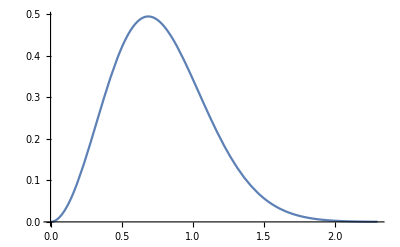

```mathematica
Plot[
Re[(-I^l 4 Pi) Exp[-γm R^2]  Exp[-γn r^2]
 ((A-1) R Exp[-igam2NIEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet2NIEx[A,a,Λ] R r]  r Exp[-ialf2NIEx[A,a,Λ] R^2]+(R Exp[-igam3NIarmEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIarmEx[A,a,Λ] R r]  r Exp[-ialf3NIarmEx[A,a,Λ] R^2]+R Exp[-igam3NIstarEx[A,a,Λ] r^2] SphericalBesselJ[l,I ibet3NIstarEx[A,a,Λ] R r]  r Exp[-ialf3NIstarEx[A,a,Λ] R^2]))]/.{A->5,a->1.3,l->1,Λ->1.2,r->1,γm->1.1,γn->2.1},{R,0.001,2.3},PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}]
```

```mathematica
Clear[l,r,x,α];
ftmp[l_,r_,x_,α_]:=
D[Exp[-α xx^2] SphericalBesselJ[l,I r xx],xx]/.xx->x
```

-4.64061×10^-18-0.0366585 ⅈ

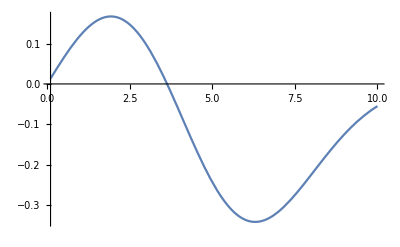

```mathematica
ftmp[1,1.1,2.1,1.1]
Plot[Re[ftmp[0,1,x,0.1]],{x,0.1,10}]
```

```mathematica
Assuming[α∈Reals&&α>0&&β∈Reals&&β>0&&γ∈Reals&&γ>0&&ωm∈Reals&&ωm>0&&ωn∈Reals&&ωn>0,
Integrate[Exp[-(α+ωm) (x1^2+y1^2+z1^2)-(γ+ωn) (x2^2+y2^2+z2^2)-β (x1 x2+y1 y2+z1 z2)],{x1,-Infinity,Infinity},{y1,-Infinity,Infinity},{z1,-Infinity,Infinity},{x2,-Infinity,Infinity},{y2,-Infinity,Infinity},{z2,-Infinity,Infinity}]
]
```

ConditionalExpression[(16 π^3 (γ+ωn))/(√(-β^2+4 (α+ωm) (γ+ωn)) Abs[γ+ωn] Abs[2 β^2-8 (α+ωm) (γ+ωn)]),γ+ωn<0]